#### Load MaTeX`

```mathematica
<<MaTeX`;
SetOptions[MaTeX,Magnification-> 2.2,"Preamble"->{"\\usepackage[dvipsnames]{xcolor}","\\definecolor{mygreen}{rgb}{0,0.45,0}","\\definecolor{mygreen2}{rgb}{0,0.8,0}","\\definecolor{myblue}{rgb}{0,0,0.8}","\\definecolor{myblue2}{rgb}{0,0,0.45}","\\definecolor{myred}{rgb}{0.65,0,0}","\\definecolor{myred2}{rgb}{0.9,0,0}","\\definecolor{mygray}{rgb}{0.4,0.4,0.4}","\\definecolor{myorange}{rgb}{0.65,0.325,0}","\\definecolor{mypurple}{rgb}{0.5,0,0.5}","\\usepackage{tikz}","\\newcommand{\\logo}[0]{\\begin{tikzpicture}[scale=1]

  %\\clip (-0.6,0.4) rectangle (1.3,-0.3);
  \\clip (-0.6,0.4) rectangle (0.6,-0.3);
  
  \\node[] at (0,0) {${\\tt HighPT}$};
  %\\node[right] at (0.85,0.07) {\\pgftext{\\includegraphics[scale=0.035]{/Users/allwicher/Dropbox/Flavor@LHC/Analyses/cannabis.pdf}}};
  
\\end{tikzpicture}}"}];
```

#### Preamble shit for plotting [run]

```mathematica
amarillo=RGBColor["#ffcc00"]
rojo=RGBColor["#cf142b"]
azul=RGBColor["#0000F3"](*RGBColor["#00247d"]*)

Yticks[label_,mag_]:={{2250,MaTeX[If[label==True,"2250",""],Magnification->mag],{0.03,0}},
			{2200,,{0.01,0}},{2150,,{0.01,0}},{2100,,{0.01,0}},{2050,,{0.01,0}},
			{2000,MaTeX[If[label==True,"2000",""],Magnification->mag],{0.03,0}},  
			{1950,,{0.01,0}},{1900,,{0.01,0}},{1850,,{0.01,0}},{1800,,{0.01,0}},
			{1750,MaTeX[If[label==True,"1750",""],Magnification->mag],{0.03,0}},
			{1700,,{0.01,0}},{1650,,{0.01,0}},{1600,,{0.01,0}},{1550,,{0.01,0}},
			{1500,MaTeX[If[label==True,"1500",""],Magnification->mag],{0.03,0}},
			{1450,,{0.01,0}},{1400,,{0.01,0}},{1350,,{0.01,0}},{1300,,{0.01,0}},
			{1250,MaTeX[If[label==True,"1250",""],Magnification->mag],{0.03,0}},
			{1200,,{0.01,0}},{1150,,{0.01,0}},{1100,,{0.01,0}},{1050,,{0.01,0}},
			{1000,MaTeX[If[label==True,"1000",""],Magnification->mag],{0.03,0}},
			{950,,{0.01,0}},{900,,{0.01,0}},{850,,{0.01,0}},{800,,{0.01,0}},
			{750,MaTeX[If[label==True,"750",""],Magnification->mag],{0.03,0}},
			{700,,{0.01,0}},{650,,{0.01,0}},{600,,{0.01,0}},{550,,{0.01,0}},
			{500,MaTeX[If[label==True,"500",""],Magnification->mag],{0.03,0}},
			{450,,{0.01,0}},{400,,{0.01,0}},{350,,{0.01,0}},{300,,{0.01,0}}}

Xticks[l_,label_,mag_]:={
			{ l[[1]]/5+l[[3]],,{0.01,0}},
			{l[[3]],MaTeX[If[label==True,ToString[l[[3]]],""],Magnification->mag],{0.02,0}},  
			{4l[[1]]/5+l[[2]],,{0.01,0}},{3l[[1]]/5+l[[2]],,{0.01,0}},{2l[[1]]/5+l[[2]],,{0.01,0}},{ l[[1]]/5+l[[2]],,{0.01,0}},
			{l[[2]],MaTeX[If[label==True,ToString[l[[2]]],""],Magnification->mag],{0.02,0}},
			{4l[[1]]/5+l[[1]],,{0.01,0}},{3l[[1]]/5+l[[1]],,{0.01,0}},{2l[[1]]/5+l[[1]],,{0.01,0}},{ l[[1]]/5+l[[1]],,{0.01,0}},
			{l[[1]],MaTeX[If[label==True,ToString[l[[1]]],""],Magnification->mag],{0.02,0}},
			{4l[[1]]/5,,{0.01,0}},{3l[[1]]/5,,{0.01,0}},{2l[[1]]/5,,{0.01,0}},{l[[1]]/5,,{0.01,0}},
			{0.0,MaTeX[If[label==True,"0",""],Magnification->mag],{0.03,0}},
			{-4l[[1]]/5,,{0.01,0}},{-3l[[1]]/5,,{0.01,0}},{-2l[[1]]/5,,{0.01,0}},{-l[[1]]/5,,{0.01,0}},
			{-l[[1]],MaTeX[If[label==True,ToString[-l[[1]]],""],Magnification->mag],{0.02,0}},
			{-4l[[1]]/5-l[[1]],,{0.01,0}},{-3l[[1]]/5-l[[1]],,{0.01,0}},{-2l[[1]]/5-l[[1]],,{0.01,0}},{ -l[[1]]/5-l[[1]],,{0.01,0}},
			{-l[[2]],MaTeX[If[label==True,ToString[-l[[2]]],""],Magnification->mag],{0.02,0}},
			{-4l[[1]]/5-l[[2]],,{0.01,0}},{-3l[[1]]/5-l[[2]],,{0.01,0}},{-2l[[1]]/5-l[[2]],,{0.01,0}},{ -l[[1]]/5-l[[2]],,{0.01,0}},
			{-l[[3]],MaTeX[If[label==True,ToString[-l[[3]]],""],Magnification->mag],{0.02,0}}
			}

Yticks1[label_,mag_]:={
{10000,MaTeX[If[label==True,"10000",""],Magnification->mag],{0.02,0}},
{9000,MaTeX[If[label==True," ",""],Magnification->mag],{0.02,0}},
{8000,MaTeX[If[label==True," ",""],Magnification->mag],{0.02,0}},
			{7000,MaTeX[If[label==True," ",""],Magnification->mag],{0.02,0}},
			{6000,MaTeX[If[label==True," ",""],Magnification->mag],{0.02,0}},
			{5000,MaTeX[If[label==True," ",""],Magnification->mag],{0.02,0}},
			{4000,MaTeX[If[label==True," ",""],Magnification->mag],{0.02,0}},
			{3000,MaTeX[If[label==True," ",""],Magnification->mag],{0.02,0}},
			{2000,MaTeX[If[label==True,"2000",""],Magnification->mag],{0.02,0}},
			{1000,MaTeX[If[label==True,"1000",""],Magnification->mag],{0.02,0}},
			{900,MaTeX[If[label==True,"",""],Magnification->mag],{0.01,0}},{800,MaTeX[If[label==True,"",""],Magnification->mag],{0.01,0}},
			{700,MaTeX[If[label==True,"",""],Magnification->mag],{0.01,0}},{600,MaTeX[If[label==True,"",""],Magnification->mag],{0.01,0}},
			{500,MaTeX[If[label==True,"500",""],Magnification->mag],{0.02,0}},
		          {400,MaTeX[If[label==True,"",""],Magnification->mag],{0.01,0}},{300,MaTeX[If[label==True,"",""],Magnification->mag],{0.01,0}},
                            {200,MaTeX[If[label==True,"200",""],Magnification->mag],{0.01,0}}}

Xticks1[label_,mag_]:={
{1.4,MaTeX[If[label==True,"1.4",""],Magnification->mag],{0.025,0}},
{1.39,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.38,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.37,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.36,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.35,MaTeX[If[label==True," ",""],Magnification->mag],{0.025,0}},
{1.34,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.33,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.32,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.31,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.3,MaTeX[If[label==True,"1.3",""],Magnification->mag],{0.025,0}},
{1.29,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.28,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.27,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.26,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.25,MaTeX[If[label==True," ",""],Magnification->mag],{0.025,0}},
{1.24,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.23,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.22,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.21,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.2,MaTeX[If[label==True,"1.2",""],Magnification->mag],{0.025,0}},
{1.19,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.18,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.17,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.16,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.15,MaTeX[If[label==True," ",""],Magnification->mag],{0.025,0}},
{1.14,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.13,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.12,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.11,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.1,MaTeX[If[label==True,"1.1",""],Magnification->mag],{0.025,0}},
{1.09,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.08,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.07,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.06,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.05,MaTeX[If[label==True," ",""],Magnification->mag],{0.025,0}},
{1.04,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.03,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.02,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},{1.01,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
		          {1.0,MaTeX[If[label==True,"1.0",""],Magnification->mag],{0.025,0}}
			}


Xticks2[label_,mag_]:={
{1.05,MaTeX[If[label==True,"1.05",""],Magnification->mag],{0.025,0}},
{1.048,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.046,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.044,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.042,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.04,MaTeX[If[label==True,"1.04",""],Magnification->mag],{0.025,0}},
{1.038,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.036,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.034,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.032,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.03,MaTeX[If[label==True,"1.03",""],Magnification->mag],{0.025,0}},
{1.028,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.026,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.024,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.022,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.02,MaTeX[If[label==True,"1.02",""],Magnification->mag],{0.025,0}},
{1.018,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.016,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.014,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.012,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.01,MaTeX[If[label==True,"1.01",""],Magnification->mag],{0.025,0}},
{1.008,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.006,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.004,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.002,MaTeX[If[label==True," ",""],Magnification->mag],{0.01,0}},
{1.0,MaTeX[If[label==True,"1.0",""],Magnification->mag],{0.025,0}}
			}

ClippedEpi[ll_,linear_]:=If[linear,
	              {{Directive[{Thickness[0.003],Black}],Line[{Scaled[{0,0}],Scaled[{0,1}]}],Directive[{Thickness[0.007],Black}],Line[{Scaled[{0.05,0.925}],Scaled[{0.125,0.925}]}],Directive[{Thickness[0.007],Black,Dashed}],Line[{Scaled[{0.05,0.85}],Scaled[{0.125,0.85}]}]}, 
                   Text[MaTeX["\\mathcal{O}(\\Lambda^{-2})",Magnification->1.2],Scaled[{0.25,0.925}],Center],
                   Text[MaTeX["\\mathcal{O}(\\Lambda^{-4})",Magnification->1.2],Scaled[{0.25,0.85}],Center],
                   Text[MaTeX["pp\\to "<>ll,Magnification->1.4],Scaled[{0.85,0.95}],Center]},
		{{Directive[{Thickness[0.003],Black}],Line[{Scaled[{0,0}],Scaled[{0,1}]}],Directive[{Thickness[0.007],Black}],Line[{Scaled[{0.05,0.925}],Scaled[{0.125,0.925}]}]}, 
                   Text[MaTeX["\\mathcal{O}(\\Lambda^{-4})",Magnification->1.2],Scaled[{0.25,0.925}],Center],
                   Text[MaTeX["pp\\to "<>ll,Magnification->1.4],Scaled[{0.85,0.95}],Center]}
];
```

RGBColor[1., 0.8, 0.]

RGBColor[0.8117647058823529, 0.0784313725490196, 0.16862745098039217]

RGBColor[0., 0., 0.9529411764705882]

```mathematica
t[a_,b_,c_,d_,e_, f_, g_,h_]:={{a,MaTeX[ToString[a],Magnification->1.2],{0.02,0}},
                   {b,MaTeX[ToString[b],Magnification->1.2],{0.02,0}},
		{c,MaTeX[ToString[c],Magnification->1.2],{0.02,0}},
		{d,MaTeX[ToString[d],Magnification->1.2],{0.02,0}},
		{e,MaTeX[ToString[e],Magnification->1.2],{0.02,0}},
		{f,MaTeX[ToString[f],Magnification->1.2],{0.02,0}},
		{g,MaTeX[ToString[g],Magnification->1.2],{0.02,0}},
                  {h,MaTeX[ToString[h],Magnification->1.2],{0.02,0}}}
tDummy[a_,b_,c_,d_,e_, f_, g_, h_]:={{a,MaTeX[" ",Magnification->1.2],{0.02,0}},
                   {b,MaTeX[" ",Magnification->1.2],{0.02,0}},
		{c,MaTeX[" ",Magnification->1.2],{0.02,0}},
		{d,MaTeX[" ",Magnification->1.2],{0.02,0}},
		{e,MaTeX[" ",Magnification->1.2],{0.02,0}},
		{f,MaTeX[" ",Magnification->1.2],{0.02,0}},
                  {g,MaTeX[" ",Magnification->1.2],{0.02,0}},
                  {h,MaTeX[" ",Magnification->1.2],{0.02,0}}}
```

```mathematica
ddee=Drop[Import["/Users/dario/Dropbox/GitHub/HighPT/HighPT/LHC_searches/di-electron_CMS_2103_02708/SMEFT/FVLL_00_dd_ee_Z_Z.dat"],14,3];
ssee=Drop[Import["/Users/dario/Dropbox/GitHub/HighPT/HighPT/LHC_searches/di-electron_CMS_2103_02708/SMEFT/FVLL_00_ss_ee_Z_Z.dat"],14,3];
bbee=Drop[Import["/Users/dario/Dropbox/GitHub/HighPT/HighPT/LHC_searches/di-electron_CMS_2103_02708/SMEFT/FVLL_00_bb_ee_Z_Z.dat"],14,3];

ddμμ=Drop[Import["/Users/dario/Dropbox/GitHub/HighPT/HighPT/LHC_searches/di-muon_CMS_2103_02708/SMEFT/FVLL_00_dd_mumu_Z_Z.dat"],14,3];
ssμμ=Drop[Import["/Users/dario/Dropbox/GitHub/HighPT/HighPT/LHC_searches/di-muon_CMS_2103_02708/SMEFT/FVLL_00_ss_mumu_Z_Z.dat"],14,3];
bbμμ=Drop[Import["/Users/dario/Dropbox/GitHub/HighPT/HighPT/LHC_searches/di-muon_CMS_2103_02708/SMEFT/FVLL_00_bb_mumu_Z_Z.dat"],14,3];


ddττ=Drop[Import["/Users/dario/Dropbox/GitHub/HighPT/HighPT/LHC_searches/di-tau_ATLAS_2002_12223/SMEFT/FVLL_00_dd_tata_Z_Z.dat"],14,3];
ssττ=Drop[Import["/Users/dario/Dropbox/GitHub/HighPT/HighPT/LHC_searches/di-tau_ATLAS_2002_12223/SMEFT/FVLL_00_ss_tata_Z_Z.dat"],14,3];
bbττ=Drop[Import["/Users/dario/Dropbox/GitHub/HighPT/HighPT/LHC_searches/di-tau_ATLAS_2002_12223/SMEFT/FVLL_00_bb_tata_Z_Z.dat"],14,3];
```

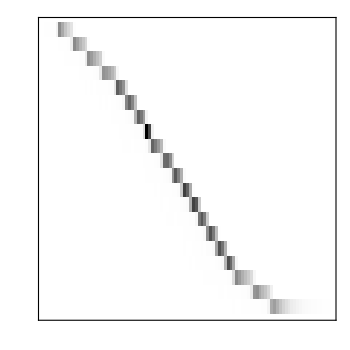
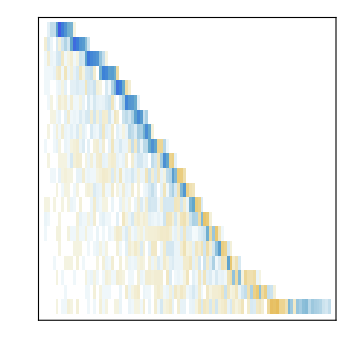
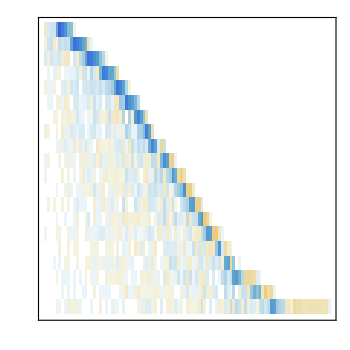
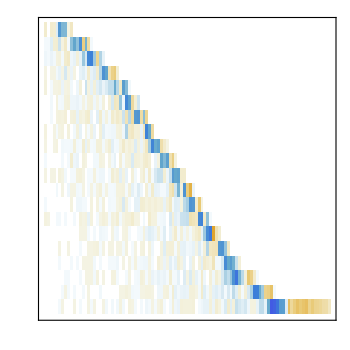

```mathematica
{Plotddee=ArrayPlot[ddee, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1(*ColorFunction->ColorData[{"GrayTones","Reverse"}]*),
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to ee",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[1,3,6,9,12,15,18,21 ],tDummy[1,3,6,9,12,15,18,21]},{tDummy[1,16,32, 48,64,80,96,112],t[1,16,32, 48,64,80,96,112
]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["K_{ij}\,(m_{ee}|\,m_{ee})",Magnification->1.75]}],
MatrixPlot[ddee-ssee, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1,
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[1,3,6,9,12,15,18,21],tDummy[1,3,6,9,12,15,18,21]},{tDummy[1,16,32, 48,64,80,96,112],t[1,16,32, 48,64,80,96,112]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["[K_{ij}]_{dd}-[K_{ij}]_{ss}",Magnification->1.75]}],
MatrixPlot[ddee-bbee, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1,
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to ee",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[1,3,6,9,12,15,18,21],tDummy[1,3,6,9,12,15,18,21]},{tDummy[1,16,32, 48,64,80,96,112],t[1,16,32, 48,64,80,96,112]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["[K_{ij}]_{dd}-[K_{ij}]_{bb}",Magnification->1.75]}],
MatrixPlot[ssee-bbee, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1,
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to ee",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[1,3,6,9,12,15,18,21],tDummy[1,3,6,9,12,15,18,21]},{tDummy[1,16,32, 48,64,80,96,112],t[1,16,32, 48,64,80,96,112]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["[K_{ij}]_{ss}-[K_{ij}]_{bb}",Magnification->1.75]}]
}
```

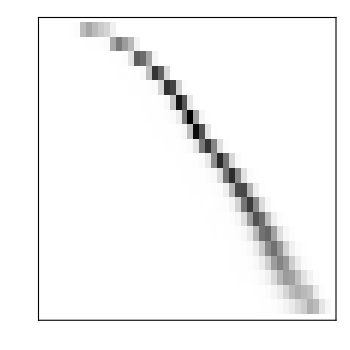
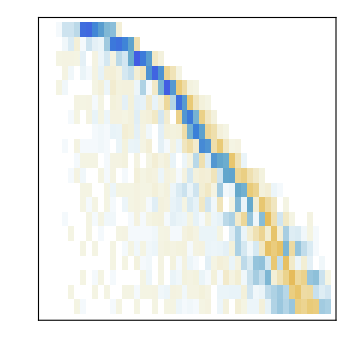
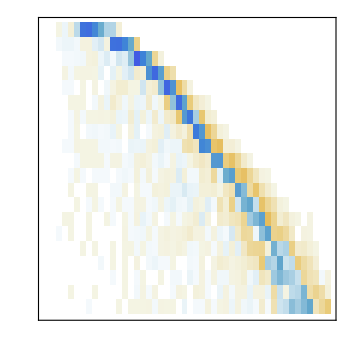
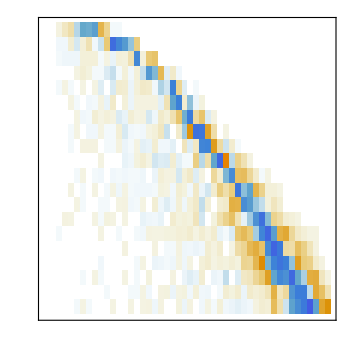

```mathematica
{Plotddμμ=ArrayPlot[ddμμ, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1(*ColorFunction->ColorData[{"GrayTones","Reverse"}]*),
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[1,3,6,9,12,15,18,21 ],tDummy[1,3,6,9,12,15,18,21]},{tDummy[1,8,16,24,32, 40,48,56],t[1,8,16,24,32, 40,48,56
]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["K_{ij}\,(m_{\\mu\\mu}|\,m_{\\mu\\mu})",Magnification->1.75]}],
MatrixPlot[ddμμ-ssμμ, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1,
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[1,3,6,9,12,15,18,21],tDummy[1,3,6,9,12,15,18,21]},{tDummy[1,8,16,24,32, 40,48,56],t[1,8,16,24,32, 40,48,56]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["[K_{ij}]_{dd}-[K_{ij}]_{ss}",Magnification->1.75]}],
MatrixPlot[ddμμ-bbμμ, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1,
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[1,3,6,9,12,15,18,21],tDummy[1,3,6,9,12,15,18,21]},{tDummy[1,8,16,24,32, 40,48,56],t[1,8,16,24,32, 40,48,56]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["[K_{ij}]_{dd}-[K_{ij}]_{bb}",Magnification->1.75]}],
MatrixPlot[ssμμ-bbμμ, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1,
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to \\mu\\mu",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[1,3,6,9,12,15,18,21],tDummy[1,3,6,9,12,15,18,21]},{tDummy[1,8,16,24,32, 40,48,56],t[1,8,16,24,32, 40,48,56]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["[K_{ij}]_{ss}-[K_{ij}]_{bb}",Magnification->1.75]}]
}
```

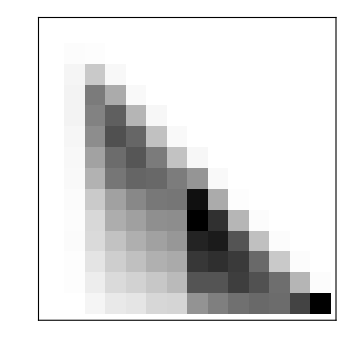
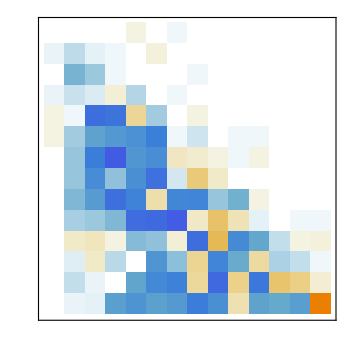
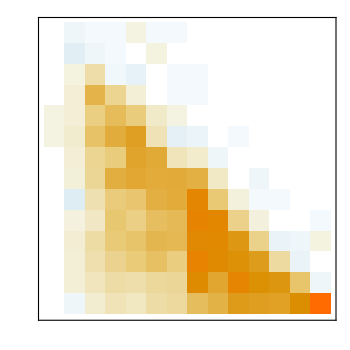
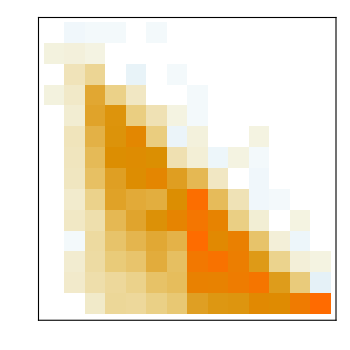

```mathematica
{Plotddττ=ArrayPlot[ddττ, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1(*ColorFunction->ColorData[{"GrayTones","Reverse"}]*),
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to \\tau\\tau",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[2,4,6,8,10,12,14,16],tDummy[2,4,6,8,10,12,14,16]},{tDummy[2,4,6,8,10,12,14,16],t[2,4,6,8,10,12,14,16]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["K_{ij}\,(m_T^{\\mathrm{tot}}|\,m_{\\tau\\tau})",Magnification->1.75]}],
MatrixPlot[ddττ-ssττ, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1(*ColorFunction->ColorData[{"GrayTones","Reverse"}]*),
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to \\tau\\tau",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[2,4,6,8,10,12,14,16 ],tDummy[2,4,6,8,10,12,14,16]},{tDummy[2,4,6,8,10,12,14,16],t[2,4,6,8,10,12,14,16]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["[K_{ij}]_{dd}-[K_{ij}]_{ss}",Magnification->1.75]}],
MatrixPlot[ddττ-bbττ, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1,
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to \\tau\\tau",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[2,4,6,8,10,12,14,16],tDummy[2,4,6,8,10,12,14,16]},{tDummy[2,4,6,8,10,12,14,16],t[2,4,6,8,10,12,14,16]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["[K_{ij}]_{dd}-[K_{ij}]_{bb}",Magnification->1.75]}],
MatrixPlot[ssττ-bbττ, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1,
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to \\tau\\tau",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[2,4,6,8,10,12,14,16],tDummy[2,4,6,8,10,12,14,16]},{tDummy[2,4,6,8,10,12,14,16],t[2,4,6,8,10,12,14,16]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["[K_{ij}]_{ss}-[K_{ij}]_{bb}",Magnification->1.75]}]}
```

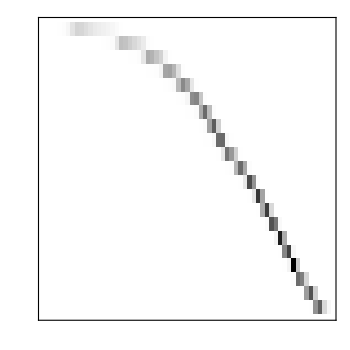

```mathematica
udeν=Drop[Import["/Users/dario/Dropbox/GitHub/HighPT/example_notebooks/FVLL_00_ud_eve_W_W.dat"] ,14,3];
Plotudeν=ArrayPlot[udeν, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1(*ColorFunction->ColorData[{"GrayTones","Reverse"}]*),
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to e\\nu",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[1,3,6,9,12, 15,18,21],tDummy[1,3,6,9,12, 15,18,21]},{tDummy[1,10,20,30,40, 50,60,70],t[1,10,20,30,40, 50,60,70]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["K_{ij}\,(m_T\,|\, p_T)",Magnification->1.75]}]
```

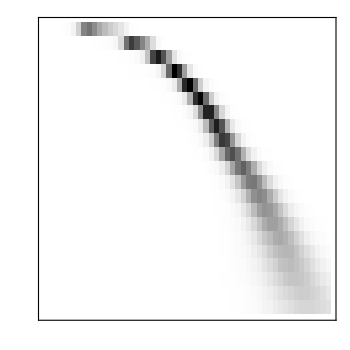

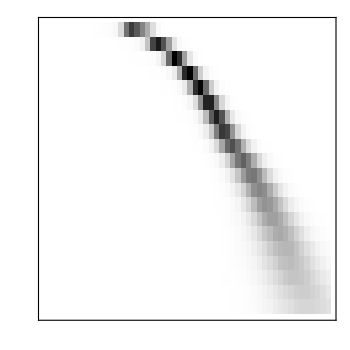

```mathematica
udμν=Drop[Import["/Users/dario/Dropbox/GitHub/HighPT/example_notebooks/FVLL_00_ud_muvm_W_W.dat"] ,14,3];
Plotudμν=ArrayPlot[udμν, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1(*ColorFunction->ColorData[{"GrayTones","Reverse"}]*),
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to \\mu\\nu",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[1,3,6,9,12, 15,18,21],tDummy[1,3,6,9,12, 15,18,21]},{tDummy[1,10,20,30,40, 50,60,70],t[1,10,20,30,40, 50,60,70]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["K_{ij}\,(m_T\,|\, p_T)",Magnification->1.75]}]
```

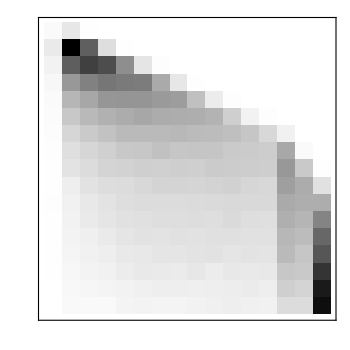

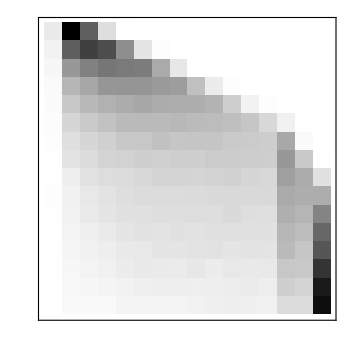

```mathematica
udτν=Drop[Import["/Users/dario/Dropbox/GitHub/HighPT/example_notebooks/FVLL_00_ud_tavt_W_W.dat"] ,14,3];
Plotudτν=ArrayPlot[udτν, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1(*ColorFunction->ColorData[{"GrayTones","Reverse"}]*),
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to \\tau\\nu",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[1,3,6,9,12, 15,18,21],tDummy[1,3,6,9,12, 15,18,21]},{tDummy[1,3,6,9,12, 15,18,21],t[1,3,6,9,12, 15,18,21]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["K_{ij}\,\,(m_T\,|\, p_T)",Magnification->1.75]}]
```

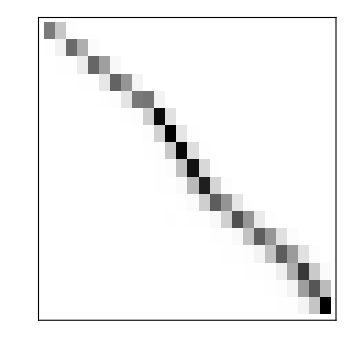

```mathematica
uuemu=Drop[Import["/Users/dario/Dropbox/GitHub/HighPT/example_notebooks/FVLL_00_uu_emu_Z_Z.dat"] ,14,3];
Plotuuemu=ArrayPlot[uuemu, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1(*ColorFunction->ColorData[{"GrayTones","Reverse"}]*),
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to e\\mu",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[2,4,6, 8,10,12,14,16],tDummy[2,4,6, 8,10,12,14,16]},{tDummy[1,4,8,12, 16,20,24,28],t[1,4,8,12, 16,20,24,28]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["K_{ij}\,(m_{e\\mu}\,|\, m_{e\\mu})",Magnification->1.75]}]
```

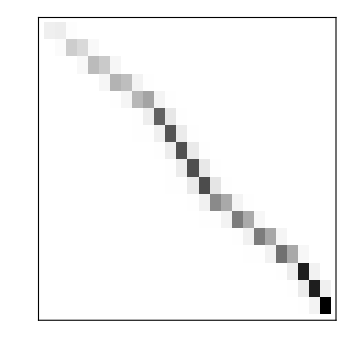

```mathematica
uueta=Drop[Import["/Users/dario/Dropbox/GitHub/HighPT/example_notebooks/FVLL_00_uu_eta_Z_Z.dat"] ,14,3];
Plotuueta=ArrayPlot[uueta, Frame->{True,True,True,True},ImageSize->350,AspectRatio->1(*ColorFunction->ColorData[{"GrayTones","Reverse"}]*),
FrameStyle->Directive[Black,Thickness[0.003]],Epilog->Text[MaTeX["pp\\to e\\tau",Magnification->1.4],Scaled[{0.85,0.925}],Center],
FrameTicks->{ {t[2,4,6, 8,10,12,14,16],tDummy[2,4,6, 8,10,12,14,16]},{tDummy[1,4,8,12, 16,20,24,28],t[1,4,8,12, 16,20,24,28]} },
FrameLabel->{MaTeX[" ",Magnification->1.75],MaTeX["K_{ij}\,(m_{e\\tau}\,|\, m^{\\mathrm {col}}_{e\\tau})",Magnification->1.75]}]
```

```mathematica
"
```

```mathematica
(*Export["K_ee.pdf",Rasterize[Plotddee,ImageResolution->400]];
Export["K_mumu.pdf",Rasterize[Plotddμμ,ImageResolution->400]];
Export["K_tata.pdf",Rasterize[Plotddττ,ImageResolution->400]];*)

Export["/Users/dario/Dropbox/GitHub/HighPT/example_notebooks/K_eve.pdf",Rasterize[Plotudeν,ImageResolution->400]];
Export["/Users/dario/Dropbox/GitHub/HighPT/example_notebooks/K_muvm.pdf",Rasterize[Plotudμν,ImageResolution->400]];
Export["/Users/dario/Dropbox/GitHub/HighPT/example_notebooks/K_tavt.pdf",Rasterize[Plotudτν,ImageResolution->400]];
(*
Export["K_emu.pdf",Rasterize[Plotddemu,ImageResolution->400]];
Export["K_eta.pdf",Rasterize[Plotuueta,ImageResolution->400]];
Export["K_muta.pdf",Rasterize[Plotuumuta,ImageResolution->400]];*)
```

```mathematica
549+472
```

1021

```mathematica
355+66
```

421